Total ask vol:29143

Total bid vol:31901

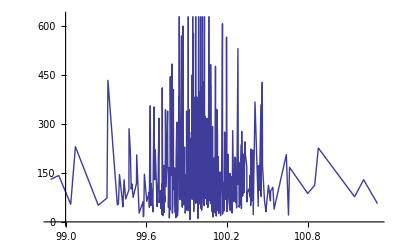

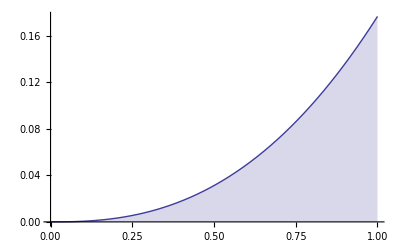

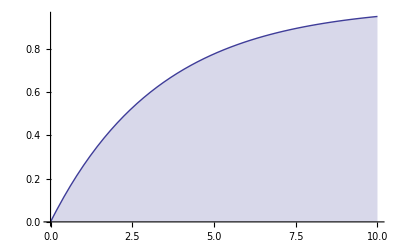

```mathematica
ClearAll[startAsk, startBid,tick, noOfOrders ,generateOrder, orders, cumVol];

tick = 0.001;
startAsk = 100;
startBid = startAsk-tick;
noOfOrders = 500;

generateOrder[startBid_,startAsk_, tick_ ] := Module[{side, size, ticks, price},
side = RandomVariate[BernoulliDistribution[0.5]]; (*0-bid, 1-ask*)
(*ticks=RandomVariate[PowerDistribution[1,0.5]];*)
(*ticks = RandomVariate[HalfNormalDistribution[0.5]];*)
ticks=RandomVariate[ExponentialDistribution[5]];
size = Round[RandomVariate[LogNormalDistribution[4.5,0.8] ]];
price =If[side == 1, startAsk+ticks ,startBid-ticks]; 
{Round[price,tick],size, side}
];

orders =Sort[ Table[generateOrder[startBid, startAsk, 0.001], {noOfOrders }],#[[1]]>#2[[1]]&];
cumVol={#[[1]][[1]],Total[#[[2]]&/@#]}&/@GatherBy[orders,#[[1]]&];
Print["Total ask vol:"<>ToString[Total[#[[2]]&/@Select[orders,#[[3]]==1&]]]];
Print["Total bid vol:"<>ToString[Total[#[[2]]&/@Select[orders,#[[3]]==0&]]]];
Print[Show[ListLinePlot[cumVol]]];
Export["/Users/jakubkozlowski/Desktop/orders.csv",orders];

Plot[CDF[PowerDistribution[0.5,2.5],x],{x,0,1},Filling->Axis,Exclusions->None]
Plot[CDF[ExponentialDistribution[0.3],x],{x,0,10},Filling->Axis,Exclusions->None]
```